## Setup

```mathematica
expandParams={x->(c kon)/koff,g->koff/kf};
cmap=ColorData[97,"ColorList"];

bigrad=Table[ColorData["ThermometerColors",i],{i,0,1,0.125}];

(* From: https://mathematica.stackexchange.com/questions/174124/extract-colorrange-of-contourplot *)
Clear[legendExtract];
Options[legendExtract]={"RGBasReal"->False};
legendExtract[plot_Legended,OptionsPattern[]]:=Module[{legend=plot[[2,1]],colordata,range,out},(*Extract colorfunction used in plot and the range of values used in the color scaling*){colordata,range}=legend[[1]]/.{b_Blend&:>b[[1]]};
(*Create list of values and colors used in legend*)out={#,ColorData[colordata][Rescale[#,range]]}&/@legend[[2]]/.{{y_Real,_}:>y};
(*If desired,output RGB values as real numbers instead of swatches*)If[OptionValue["RGBasReal"]==True,out/.{RGBColor[vals__]:>vals},out]]

contourcmap=Table[legendExtract[ContourPlot[Min[Cos[x]+Cos[y],1.5],{x,0,4Pi},{y,0,4Pi},PlotLegends->Automatic]][[i,2]],{i,1,7}];
categoricalcmap=ColorData[3,"ColorList"];
clist={categoricalcmap[[1]],categoricalcmap[[4]],categoricalcmap[[6]]};
```

### Multimers

#### Homodimer

```mathematica
homdimsol=T/.Solve[{Kb==(L R)/B,Kt==(R B)/T,Rt==R+B+2T},{R,B,T}][[2]]//FullSimplify;
HomoDimer[L_,Rt_,Kb_,Kt_]:=(Kt (Kb+L)^2+4 Kb L Rt-(Kb+L) √(Kt (Kt (Kb+L)^2+8 Kb L Rt)))/(8 Kb L);
HomoDimerB[L_,Rt_,Kb_,Kt_]:=(-Kb Kt-Kt L+√(Kt (Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb);
HomoDiMax[Rt_,Kb_,Kt_]:=(Kb (Kt+Rt)-√(Kb^2 Kt (Kt+2 Rt)))/(2 Kb);

μDi=kp t HomoDimer[c,Rt,koff/kon ,(2koff)/kf];
```

```mathematica
Assuming[KD Rt>0,Simplify[μDi/(Rt/2)/.{c->KD,kf->(kon KD)/(g Rt),koff->kon KD}]]
```

(1+2 g-2 √(g (1+g))) kp t

Derivation of Eq. 7 in the paper:

```mathematica
kp t HomoDimer[c,Rt,koff/kon,2 koff/kf]
```

(kon kp ((2 koff (c+koff/kon)^2)/kf+(4 c koff Rt)/kon-√2 (c+koff/kon) √((koff ((2 koff (c+koff/kon)^2)/kf+(8 c koff Rt)/kon))/kf)) t)/(8 c koff)

```mathematica
(kp t kon)/(8 c koff)koff^2/kon^2 Rt(kon^2/(koff^2 Rt)(2 koff c^2(1+1/x)^2)/kf+kon^2/(koff^2 Rt)(4 c koff Rt)/kon-√2 kon^2/(koff^2 Rt)c(1+1/x) √((koff ((2 koff c^2(1+1/x)^2)/kf+(8 c koff Rt)/kon))/kf)) 

(kp t Rt)/(8x)(2 g (1+x)^2+4x-√2 kon/(koff Rt)(1+x) √((koff ((2 koff c^2(1+1/x)^2)/kf+(8 c koff Rt)/kon))/kf)) 


(kp t Rt)/(8x)(2 g (1+x)^2+4x-√2 (1+x) √(g (kon^2/(koff^2 Rt)(2 koff c^2(1+1/x)^2)/kf+kon^2/(koff^2 Rt)(8 c koff Rt)/kon))) 

(kp t Rt)/(8x)(2 g (1+x)^2+4x-(1+x) √(2g (2 g (1+x)^2+8x))) 

(kp t Rt)/(8x)(2 g (1+x)^2+4x-2(1+x) √(g (g (1+x)^2+4x)))
```

(koff kp Rt t ((4 c kon)/koff-(√2 c kon^2 √((koff ((8 c koff Rt)/kon+(2 c^2 koff (1+1/x)^2)/kf))/kf) (1+1/x))/(koff^2 Rt)+(2 c^2 kon^2 (1+1/x)^2)/(kf koff Rt)))/(8 c kon)

(kp Rt t (4 x-(√2 kon √((koff ((8 c koff Rt)/kon+(2 c^2 koff (1+1/x)^2)/kf))/kf) (1+x))/(koff Rt)+2 g (1+x)^2))/(8 x)

(kp Rt t (4 x-√2 √(g ((8 c kon)/koff+(2 c^2 kon^2 (1+1/x)^2)/(kf koff Rt))) (1+x)+2 g (1+x)^2))/(8 x)

(kp Rt t (4 x+2 g (1+x)^2-√2 (1+x) √(g (8 x+2 g (1+x)^2))))/(8 x)

(kp Rt t (4 x+2 g (1+x)^2-2 (1+x) √(g (4 x+g (1+x)^2))))/(8 x)

And the maximum occurs at:

```mathematica
Solve[D[(kp t Rt)/(8x)(2 g (1+x)^2+4x-2(1+x) √(g (g (1+x)^2+4x))) ,x]==0,x]
```

{{x→1}}

```mathematica
(kp t Rt)/(8x)(2 g (1+x)^2+4x-2(1+x) √(g (g (1+x)^2+4x))) /.x->1//Simplify
```

-1/2 (-1-2 g+2 √(g (1+g))) kp Rt t

```mathematica
(kp Rt t)/2 (1+2 g-2 √(g (1+g)))
```

1/2 (1+2 g-2 √(g (1+g))) kp Rt t

```mathematica
(* Code Derivation of Variance *)
```

The Blackwell–Girshick equation tells us that the variance of a sum of a random number N of random variables X_i
 Y=Σ_i^N X_i
is given by:
Var(Y)= E[N]Var(X_0)+Var(N)(E[X_0])^2

For us, these terms have the following analogues:
Var(N)=1/(4/(Rt-HomoDimerB[c,Rt,koff/kon ,(2koff)/kf]-2*HomoDimer[c,Rt,koff/kon ,(2koff)/kf])+1/HomoDimer[c,Rt,koff/kon ,(2koff)/kf])
E[X_0]= kp t
E[N]=HomoDimer[c,Rt,koff/kon ,koff/kf]
Var[X_0]=kp t

#### Homotrimer

```mathematica
Tri[c_,Rt_,Kb_,Kt_,Kq_]:=(-2 2^(2/3) c^4 Kq^2 (32 Kq^2-144 Kq Kt+135 Kt^2)-3 2^(1/3) √3 √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))) (9 2^(1/3) Kb Kt+2 (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3))+2^(1/3) c^3 Kq (9 2^(1/3) Kb Kt (32 Kq^2-60 Kq Kt+72 Kq Rt-81 Kt Rt)+2 (16 Kq^2-54 Kq Kt+27 Kt^2) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3))-c^2 Kq (27 2^(2/3) Kb^2 Kt^2 (10 Kq+27 Rt)-54 2^(1/3) Kb Kt (-2 Kq+2 Kt-3 Rt) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3)+4 (4 Kq-9 Kt) (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3))+3 c (8 2^(2/3) √3 Kq √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt))))-9 2^(2/3) √3 Kt √(c^3 Kq^2 Kt (-4 c^3 Kq (Kq-3 Kt) Kt+12 Kb^3 Kq Kt^2+c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))-4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt))))+18 2^(1/3) Kb^2 Kq Kt^2 (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(1/3)+12 Kb Kq Kt (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3)+18 Kb Kt Rt (2 c^3 Kq^2 (-8 Kq+27 Kt)+27 c^2 Kb Kq Kt (2 Kq+9 Rt)+9 √3 √(-c^3 Kq^2 Kt (4 c^3 Kq (Kq-3 Kt) Kt-12 Kb^3 Kq Kt^2-c Kb^2 Kt (-4 Kq^2+243 Rt^2+36 Kq (Kt+3 Rt))+4 c^2 Kb Kq (-9 Kt (Kt+3 Rt)+2 Kq (Kt+4 Rt)))))^(2/3)))/(162 c Kb Kt (-16 c^3 Kq^3+54 c^3 Kq^2 Kt+54 c^2 Kb Kq^2 Kt+243 c^2 Kb Kq Kt Rt+√(c^3 Kq^2 (4 Kq (-4 c Kq+9 c Kt+9 Kb Kt)^3+c (2 c Kq (-8 Kq+27 Kt)+27 Kb Kt (2 Kq+9 Rt))^2)))^(2/3));


TriRfree[L_,Rt_,Kd_,Γd_,δd_]=-(2 δd)/9-(2^(1/3) (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd)))/(9 L (243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3+√((243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3)^2+4 (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd))^3))^(1/3))+1/(9 2^(1/3) L)(243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3+√((243 Kd L^2 Rt Γd δd+54 Kd L^2 Γd δd^2+54 L^3 Γd δd^2-16 L^3 δd^3)^2+4 (-4 L^2 δd^2+9 L (Kd Γd δd+L Γd δd))^3))^(1/3);
```

```mathematica
TriMax[Rt_,K1_,K3_,K4_]:=Module[{t1,maxC,c1=Table[10^Logc,{Logc,-16,16,0.1}]},
t1=Table[Tri[c1[[i]],Rt,K1,K3,K4],{i,1,Length[c1]}];
maxC=c1[[Flatten[Position[t1,Max[t1]]][[1]]]];
Tri[maxC,Rt,K1,K3,K4]
]
```

```mathematica
μTri=kp t Tri[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf];
VarTri=1/(9/TriRfree[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf]+1/Tri[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf]);
ΣTri=μTri+(kp t)^2 VarTri;
```

#### Homotetramer

```mathematica
(* Derivation *)
homsoltet=Solve[{
Kb==(c R)/B,
Kt== (B R)/T,
Kq==(T R)/Q,
Ktet==(Q R)/Tet,
Rt==R+B+2T+3Q+4Tet},

{R,B,T,Q,Tet}][[2]];
TetAct[CTEST_,RtTEST_,KbTEST_,KtTEST_,KqTEST_,KtetTEST_]:=Tet/.homsoltet/.{c->CTEST,Rt->RtTEST,Kb->KbTEST,Kt->KtTEST,Kq->KqTEST,Ktet->KtetTEST}


TetMax[Rt_,K1_,K3_,K4_,K5_]:=Module[{t1,maxC,c1=Table[10^Logc,{Logc,-16,16,0.1}]},
t1=Table[TetAct[c1[[i]],Rt,K1,K3,K4,K5],{i,1,Length[c1]}];
maxC=c1[[Flatten[Position[t1,Max[t1]]][[1]]]];
TetAct[maxC,Rt,K1,K3,K4,K5]
]

TetRfree[CTEST_,RtTEST_,KbTEST_,KtTEST_,KqTEST_,KtetTEST_]:=R/.homsoltet/.{c->CTEST,Rt->RtTEST,Kb->KbTEST,Kt->KtTEST,Kq->KqTEST,Ktet->KtetTEST}
```

```mathematica
μTet=kp t TetAct[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf,(4koff)/kf];

VarTet=1/(16/TetRfree[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf,(4koff)/kf]+1/TetAct[c,Rt,koff/kon ,(2koff)/kf,(3koff)/kf,(4koff)/kf]);
ΣTet=μTet+(kp t)^2 VarTet;
```

#### Mixed Multimers

These are designed to compare with the adaptive sorting model

```mathematica
DiMixed[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
L1free[t]==L1-(C0[t]+C1[t]),
L2free[t]==L2-(D0[t]+D1[t]),
Rfree[t]==R-(C0[t]+2C1[t]+D0[t]+2D1[t]),
C0'[t]==κ L1free[t]Rfree[t]-(Rfree[t]ϕ+ν1)C0[t],
C1'[t]==ϕ Rfree[t]C0[t]-ν1 C1[t],
D0'[t]==κ L2free[t]Rfree[t]-(Rfree[t]ϕ+ν2)D0[t],
D1'[t]==ϕ Rfree[t]D0[t]-ν2 D1[t],
S[0]==0,C0[0]==0,C1[0]==0,D0[0]==0,D1[0]==0,L1free[0]==L1,L2free[0]==L2,Rfree[0]==R};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C1,D1},{t,1,tend}];
(C1[tend]+D1[tend]/.sol)[[1]]
]
TriMixed[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
L1free[t]==L1-(C0[t]+C1[t]+C2[t]),
L2free[t]==L2-(D0[t]+D1[t]+D2[t]),
Rfree[t]==R-(C0[t]+2C1[t]+3C2[t]+D0[t]+2D1[t]+3D2[t]),
C0'[t]==κ L1free[t]Rfree[t]+ν1 C1[t]-(Rfree[t]ϕ+ν1)C0[t],
C1'[t]==ϕ Rfree[t]C0[t]+ν1 C2[t]-(Rfree[t]ϕ+ν1)C1[t],
C2'[t]==ϕ Rfree[t] C1[t]-ν1 C2[t],
D0'[t]==κ L2free[t]Rfree[t]+ν2 D1[t]-(Rfree[t]ϕ+ν2)D0[t],
D1'[t]==ϕ Rfree[t]D0[t]+ν2 D2[t]-(Rfree[t]ϕ+ν2)D1[t],
D2'[t]==ϕ Rfree[t] D1[t]-ν2 D2[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,D0[0]==0,D1[0]==0,D2[0]==0,L1free[0]==L1,L2free[0]==L2,Rfree[0]==R};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C2,D2},{t,1,tend}];
(C2[tend]+D2[tend]/.sol)[[1]]
]
```

Same ODEs, but now designed for a more traditional parameterization

```mathematica
DiMixedSimple[c1_,c2_,koff1_:1,koff2_,R_,kon_,kf_,
tend_:300]:=Module[{ASeqs,sol},
ASeqs={Rfree[t]==R-C0[t]-2 C1[t]-D0[t]-2 D1[t],
C0'[t]==c1 kon Rfree[t]-C0[t] (koff1+kf Rfree[t]),
C1'[t]==-koff1 C1[t]+kf C0[t] Rfree[t],
D0'[t]==c2 kon Rfree[t]-D0[t] (koff2+kf Rfree[t]),
D1'[t]==-koff2 D1[t]+kf D0[t] Rfree[t],
C0[0]==0,C1[0]==0,D0[0]==0,D1[0]==0,Rfree[0]==R};
sol=Quiet@NDSolve[ASeqs,{C0,D0,Rfree,C1,D1},{t,0,tend}];
Quiet[(C1[tend]+D1[tend]/.sol)]
]
```

#### Non-equilibrium Dimer Model

```mathematica
Solve[{Kb==(L R)/B,Kt E^δ21==(R B)/T,Rt==R+B+2T},{R,B,T}][[2]]//FullSimplify
```

{R→(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 L),B→(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb),T→(ⅇ^δ21 Kt (Kb+L)^2+4 Kb L Rt-Kb √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt))-L √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(8 Kb L)}

```mathematica
TNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=1/(8 Kb L)(ⅇ^δ21 Kt (Kb+L)^2+4 Kb L Rt-Kb √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt))-L √(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)));
BNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 Kb);
RfreeNonEq[L_,Rt_,Kb_,Kt_,δ21_]:=(-ⅇ^δ21 Kt (Kb+L)+√(ⅇ^δ21 Kt (ⅇ^δ21 Kt (Kb+L)^2+8 Kb L Rt)))/(4 L);
```

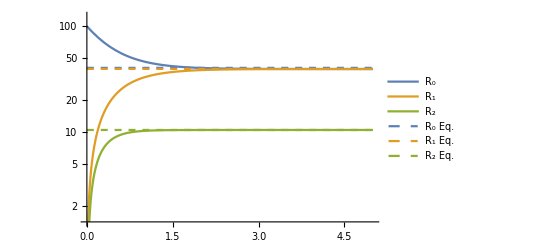

```mathematica
DimerNonEqODEs={
D[R2[t],t]==kf R0[t]R1[t]-E^δ21 koff R2[t],
D[R1[t],t]==kon c R0[t]-(koff+kf R0[t])R1[t]+E^δ21 koff R2[t],
R0[t]+R1[t]+2R2[t]==RT,
R0[0]==RT,
R1[0]==0,
R2[0]==0};
DimerNonEqSol[params_]:=NDSolve[Evaluate[DimerNonEqODEs/.params],{R0,R1,R2},{t,100}];

Show[LogPlot[Evaluate[{R0[t],R1[t],R2[t]}/.DimerNonEqSol[{kon->1,c->1,RT->100,koff->1,kf->1,δ21->5}]],{t,0,5},PlotLegends->{"R_0","R_1","R_2"}],
LogPlot[{1+RfreeNonEq[1,100,1,1,5],BNonEq[1,100,1,1,5]+0.1,TNonEq[1,100,1,1,5]},{t,0,5},PlotRange->{Automatic,{0,105}},PlotLegends->{"R_0 Eq.","R_1 Eq.","R_2 Eq."},PlotStyle->Dashed]]
```

```mathematica
μDimerNonEq=kp t TNonEq[c,RT,koff/kon,koff/kf,δ21];
σ2DimerNonEq=μDimerNonEq+(kp t)^2/(4/RfreeNonEq[c,RT,koff/kon,koff/kf,δ21]+1/TNonEq[c,RT,koff/kon,koff/kf,δ21]);
SNRDimerNonEq=μDimerNonEq/(√σ2DimerNonEq)//Simplify;
```

#### Higher N multimers

Chemical equilibrium kinetic equations give that R_i=1/(i!)(kon c)/kf((kf R0)/koff)^i 
The conservation equation can be manipulated to solve for R0:
R_T=R0+(Σ_(i=1))^(i=N+1)i 1/(i!)(kon c)/kf((kf R0)/koff)^i

```mathematica
MultGeneral[kon_,c_,koff_,kf_,RT_,Ns_]:=Module[{R0ss},
R0ss=R0/.Last[Sort[NSolve[RT==R0+Sum[i 1/(i!)(kon c)/kf((kf R0)/koff)^i,{i,1,Ns+1}],R0,Reals]]];
1/((Ns+1)!)(kon c)/kf((kf R0ss)/koff)^(Ns+1)
]
MultGeneralR0[kon_,c_,koff_,kf_,RT_,Ns_]:=Module[{R0ss},
R0ss=R0/.Last[Sort[NSolve[RT==R0+Sum[i 1/(i!)(kon c)/kf((kf R0)/koff)^i,{i,1,Ns+1}],R0,Reals]]];
R0ss
]
MultSNRGeneral[Rsol_,R0sol_,kp_,t_,Ns_]:=Module[{μ,VarR,σ},
μ=kp t Rsol;
VarR=(1/Rsol+(Ns+1)^2/R0sol)^-1;
σ=√(μ+(kp t)^2 VarR);
μ/σ//N
]
```

#### Heteromultimers

```mathematica
μ2Het=Rt/2(1+K4/Rt((IFN+K2)(IFN+K1))/(IFN K1)-√((1+K4/Rt((IFN+K2)(IFN+K1))/(IFN K1))^2-1+(Δ/Rt)^2))/.{K1->koff1/kon,K2->koff2/kon,K4->koff4/kf};
cellSA=4π 10^3;
IFNαParams={koff1->1*R1factor,kon->2*10^5,koff2->0.015*R2factor,koff4->0.29*4π*0.094*cellSA*R1factor,kf->4π*0.094*cellSA};
```

```mathematica
η2Het=(μ2Het/.{koff1->ζ koff1,koff2->ζ koff2,koff4->ζ koff4})/μ2Het;
```

```mathematica
μ2HetNonEq[params_,tend_:300]:=Module[{eqs,sol},
eqs={
D[R1f[t],t]==-kon c R1f[t]-kf B2[t] R1f[t]+koff1 B1[t]+koff4 θ T[t],
D[R2f[t],t]==-kon c R2f[t]-E^δ kf B1[t] R2f[t]+koff2 B2[t]+koff3 θ T[t],

D[B1[t],t]==kon c R1f[t]-koff1 B1[t]-E^δ kf B1[t]R2f[t]+koff3 θ T[t],
D[B2[t],t]==kon c R2f[t]-koff2 B2[t]-kf B2[t]R1f[t]+koff4 θ T[t],

D[T[t],t]==kf B2[t] R1f[t]+E^δ kf B1[t] R2f[t]-θ T[t](koff3+koff4),

R1f[0]==R1T,R2f[0]==R2T,B1[0]==0,B2[0]==0,T[0]==0}/.params;

sol=NDSolve[eqs,T,{t,0,tend}];
(T[tend]/.sol)[[1]]
];

μ2HetNonEqAlt[params_,tend_:300]:=Module[{eqs,sol},
eqs={
D[R1f[t],t]==-kon c R1f[t]-kf B2[t] R1f[t]+koff1 B1[t]+koff1 θ T[t],
D[R2f[t],t]==-kon c R2f[t]-E^δ kf B1[t] R2f[t]+koff2 B2[t]+koff2 θ T[t],

D[B1[t],t]==kon c R1f[t]-koff1 B1[t]-E^δ kf B1[t]R2f[t]+koff2 θ T[t],
D[B2[t],t]==kon c R2f[t]-koff2 B2[t]-kf B2[t]R1f[t]+koff1 θ T[t],

D[T[t],t]==kf B2[t] R1f[t]+E^δ kf B1[t] R2f[t]-θ T[t](koff1+koff2),

R1f[0]==R1T,R2f[0]==R2T,B1[0]==0,B2[0]==0,T[0]==0}/.params;

sol=NDSolve[eqs,T,{t,0,tend}];
(T[tend]/.sol)[[1]]
];
```

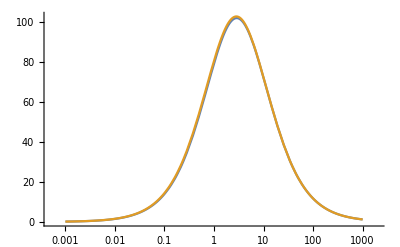

```mathematica
LogLinearPlot[{
μ2HetNonEq[{R1T->10000/2,R2T->10000/2,kon->1,kf->1/10000,koff1->2,koff2->4,koff3->8,koff4->16,θ->0.5,δ->0,c->ctest}],
μ2Het/.{Rt->R1T+R2T,Δ->R1T-R2T,IFN->c,K1->koff1/kon,K2->koff2/kon,K4->koff4/kf}/.{R1T->10000/2,R2T->10000/2,kon->1,kf->1/10000,koff2->2,koff1->4,koff4->8,koff3->16,θ->0.5,δ->0,c->ctest}},
{ctest,0.001,1000}]
```

```mathematica
μ3Het[params_,tend_:300]:=Module[{eqs,sol},
eqs={
D[R1f[t],t]==-kon c R1f[t]-kf B2[t] R1f[t]-kf B3[t] R1f[t]-kf T23[t] R1f[t]+koff1 (B1[t]+θ T12[t]+θ T13[t]+θ Q[t]),
D[R2f[t],t]==-kon c R2f[t]-kf B1[t] R2f[t]-kf B3[t] R2f[t]-kf T13[t] R2f[t]+koff2 (B2[t]+θ T12[t]+θ T23[t]+θ Q[t]),
D[R3f[t],t]==-kon c R3f[t]-kf B1[t] R3f[t]-kf B2[t] R3f[t]-kf T12[t] R3f[t]+koff3 (B3[t]+θ T13[t]+θ T23[t]+θ Q[t]),

D[B1[t],t]==kon c R1f[t]-koff1 B1[t]+koff2 θ T12[t]-kf B1[t]R2f[t]+koff3 θ T13[t]-kf B1[t]R3f[t],
D[B2[t],t]==kon c R2f[t]-koff2 B2[t]+koff1 θ T12[t]-kf B2[t]R1f[t]+koff3 θ T23[t]-kf B2[t]R3f[t],
D[B3[t],t]==kon c R3f[t]-koff3 B3[t]+koff2 θ T23[t]-kf B3[t]R2f[t]+koff1 θ T13[t]-kf B3[t]R1f[t],

D[T12[t],t]==kf B1[t] R2f[t]+kf B2[t] R1f[t]+koff3 θ Q[t]-(koff1 +koff2)θ T12[t]-kf T12[t] R3f[t],
D[T13[t],t]==kf B1[t] R3f[t]+kf B3[t] R1f[t]+koff2 θ Q[t]-(koff1 +koff3)θ T13[t]-kf T13[t] R2f[t],
D[T23[t],t]==kf B2[t] R3f[t]+kf B3[t] R2f[t]+koff1 θ Q[t]-(koff2 +koff3)θ T23[t]-kf T23[t] R1f[t],

D[Q[t],t]==kf T12[t] R3f[t]+kf T13[t] R2f[t]+kf T23[t] R1f[t]-θ Q[t](koff1+koff2+koff3),

R1f[0]==R1T,R2f[0]==R2T,R3f[0]==R3T,B1[0]==0,B2[0]==0,B3[0]==0,T12[0]==0,T13[0]==0,T23[0]==0,Q[0]==0}/.params;

sol=NDSolve[eqs,Q,{t,0,tend}];
(Q[tend]/.sol)[[1]]
];
```

```mathematica
μ4Het[params_,tend_:300]:=Module[{eqs,sol},
eqs={
D[R1f[t],t]==-kon c R1f[t]-kf R1f[t]( B2[t]+ B3[t]+B4[t]+T23[t]+T24[t]+T34[t]+Q234[t])+koff1 B1[t]+θ koff1 (T12[t]+T13[t]+T14[t]+Q123[t]+Q124[t]+Q134[t]+P[t]),
D[R2f[t],t]==-kon c R2f[t]-kf R2f[t]( B1[t]+ B3[t]+B4[t]+T13[t]+T14[t]+T34[t]+Q134[t])+koff2 B2[t]+θ koff2 (T12[t]+T23[t]+T24[t]+Q123[t]+Q124[t]+Q234[t]+P[t]),D[R3f[t],t]==-kon c R3f[t]-kf R3f[t]( B2[t]+ B1[t]+B4[t]+T12[t]+T24[t]+T14[t]+Q124[t])+koff3 B3[t]+θ koff3 (T23[t]+T13[t]+T34[t]+Q123[t]+Q234[t]+Q134[t]+P[t]),D[R4f[t],t]==-kon c R4f[t]-kf R4f[t]( B2[t]+ B3[t]+B1[t]+T23[t]+T12[t]+T13[t]+Q123[t])+koff4 B4[t]+θ koff4(T14[t]+T24[t]+T34[t]+Q124[t]+Q134[t]+Q234[t]+P[t]),

D[B1[t],t]==kon c R1f[t]-koff1 B1[t]+koff2 θ T12[t]+koff3 θ T13[t]+koff4 θ T14[t]-kf B1[t](R2f[t]+R3f[t]+R4f[t]),
D[B2[t],t]==kon c R2f[t]-koff2 B2[t]+koff1 θ T12[t]+koff3 θ T23[t]+koff4 θ T24[t]-kf B2[t](R1f[t]+R3f[t]+R4f[t]),
D[B3[t],t]==kon c R3f[t]-koff3 B3[t]+koff1 θ T13[t]+koff2 θ T23[t]+koff4 θ T34[t]-kf B3[t](R1f[t]+R2f[t]+R4f[t]),
D[B4[t],t]==kon c R4f[t]-koff4 B4[t]+koff1 θ T14[t]+koff2 θ T24[t]+koff3 θ T34[t]-kf B4[t](R1f[t]+R2f[t]+R3f[t]),

D[T12[t],t]==kf B1[t] R2f[t]+kf B2[t] R1f[t]+koff3 θ Q123[t]+koff4 θ Q124[t]-kf T12[t](R3f[t]+R4f[t])-θ T12[t](koff1+koff2),
D[T13[t],t]==kf B1[t] R3f[t]+kf B3[t] R1f[t]+koff2 θ Q123[t]+koff4 θ Q134[t]-kf T13[t](R2f[t]+R4f[t])-θ T13[t](koff1+koff3),D[T14[t],t]==kf B1[t] R4f[t]+kf B4[t] R1f[t]+koff3 θ Q134[t]+koff2 θ Q124[t]-kf T14[t](R2f[t]+R3f[t])-θ T14[t](koff1+koff4),D[T23[t],t]==kf B2[t] R3f[t]+kf B3[t] R2f[t]+koff1 θ Q123[t]+koff4 θ Q234[t]-kf T23[t](R1f[t]+R4f[t])-θ T23[t](koff2+koff3),D[T24[t],t]==kf B2[t] R4f[t]+kf B4[t] R2f[t]+koff3 θ Q234[t]+koff1 θ Q124[t]-kf T24[t](R1f[t]+R3f[t])-θ T24[t](koff2+koff4),D[T34[t],t]==kf B3[t] R4f[t]+kf B4[t] R3f[t]+koff1 θ Q134[t]+koff2 θ Q234[t]-kf T34[t](R1f[t]+R2f[t])-θ T34[t](koff3+koff4),

D[Q123[t],t]==kf T12[t] R3f[t]+kf T13[t]R2f[t]+kf T23[t]R1f[t]-θ Q123[t](koff1+koff2+koff3)-kf Q123[t]R4f[t]+koff4 θ P[t],
D[Q124[t],t]==kf T12[t] R4f[t]+kf T14[t]R2f[t]+kf T24[t]R1f[t]-θ Q124[t](koff1+koff2+koff4)-kf Q124[t]R3f[t]+koff3 θ P[t],
D[Q134[t],t]==kf T13[t] R4f[t]+kf T14[t]R3f[t]+kf T34[t]R1f[t]-θ Q134[t](koff1+koff3+koff4)-kf Q134[t]R2f[t]+koff2 θ P[t],
D[Q234[t],t]==kf T23[t] R4f[t]+kf T24[t]R3f[t]+kf T34[t]R2f[t]-θ Q234[t](koff2+koff3+koff4)-kf Q234[t]R1f[t]+koff1 θ P[t],

D[P[t],t]==kf Q123[t] R4f[t]+kf Q124[t]R3f[t]+kf Q234[t]R1f[t]+kf Q134[t]R2f[t]-θ P[t](koff1+koff2+koff3+koff4),

R1f[0]==R1T,R2f[0]==R2T,R3f[0]==R3T,R4f[0]==R4T,B1[0]==0,B2[0]==0,B3[0]==0,B4[0]==0,T12[0]==0,T13[0]==0,T14[0]==0,T23[0]==0,T24[0]==0,T34[0]==0,Q123[0]==0,Q124[0]==0,Q134[0]==0,Q234[0]==0,P[0]==0}/.params;

sol=NDSolve[eqs,P,{t,0,tend}];
(P[tend]/.sol)[[1]]
];
```

```mathematica
SHetDim=ϵ1 B1+ϵ2 B2+ϵt T-(B1+B2+T)Log[c]-1/β(Rt Log[A/Rt]+B1 Log[Rt/B1]+B2 Log[Rt/B2]+T Log[Rt^2/T]+(R1+R2+B1+B2+2T)-T Log[2]);
Solve[0==#&/@D[SHetDim,{{B1,B2,T}}],{B1,B2,T}]
```

{{B1→ConditionalExpression[ⅇ^(-β (ϵ1-Log[c])) Rt,-π<Im[β (ϵ1-Log[c])]≤π&&-π<Im[β (ϵ2-Log[c])]≤π&&-π<Im[β ϵt-β Log[c]]≤π],B2→ConditionalExpression[ⅇ^(-β (ϵ2-Log[c])) Rt,-π<Im[β (ϵ1-Log[c])]≤π&&-π<Im[β (ϵ2-Log[c])]≤π&&-π<Im[β ϵt-β Log[c]]≤π],T→ConditionalExpression[1/2 ⅇ^(1-β ϵt+β Log[c]) Rt^2,-π<Im[β (ϵ1-Log[c])]≤π&&-π<Im[β (ϵ2-Log[c])]≤π&&-π<Im[β ϵt-β Log[c]]≤π]}}

### KPR

```mathematica
(* Signal means *)
μ0= kp t x/(1+x)/.expandParams;
μ1= (kp t)/(1+g)x/(1+x)/.expandParams;
μ2=(kp t)/(1+g)^2 x/(1+x)/.expandParams;
μ3=(kp t)/(1+g)^3 x/(1+x)/.expandParams;
μ4=(kp t)/(1+g)^4 x/(1+x)/.expandParams;
μN=(kp t)/(1+g)^Ns x/(1+x)/.expandParams;
```

```mathematica
(* All variances are given for large t *)
(* Signal variances *)
Σ0=(kp t x)/(1+x)+(2 kp^2 t x)/(koff(1+x)^3)/.expandParams;

Σ1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;(*Limit of large t*)

Σ2=(kp t x ((1+g)^3 koff (1+x)^2+2 kp (1+3 g^2 (1+x)^2+g^3 (1+x)^2+g (3+2 x))))/((1+g)^5 koff (1+x)^3)/.expandParams;

Σ3=1/((1+g)^7 koff (1+x)^3)kp t x ((1+g)^4 koff (1+x)^2+2 kp (1+6 g^2 (1+x)^2+4 g^3 (1+x)^2+g^4 (1+x)^2+g (4+3 x)))/.expandParams;

Σ4=1/((1+g)^9 koff (1+x)^3)kp t x ((1+g)^5 koff (1+x)^2+2 kp (1+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5+4 x)))/.expandParams;
```

```mathematica
ΣN=(kp t x ((1+g)^(Ns+1) koff (1+x)^2+2 kp ((1+g)^(Ns+1) (1+x)^2-x (2+x+g (2+Ns+Ns x+x)))))/((1+g)^(1+2Ns) koff (1+x)^3);
(* (kp t x)/((1+x)(1+g)^Ns)+((2 kp^2 t x)/((koff+koff x)(1+g)^Ns)-(2 kp^2 t x^2 (2+x+g (2+Ns+Ns x+x)))/((1+g)^(1+2Ns) koff (1+x)^3)) *)
```

```mathematica
(* Signal sensitivity *)
η0=(μ0/.koff->δ koff)/μ0;
η1=(μ1/.koff->δ koff)/μ1;
η2=(μ2/.koff->δ koff)/μ2;
η3=(μ3/.koff->δ koff)/μ3;
η4=(μ4/.koff->δ koff)/μ4;
ηN=((kf+koff)^Ns (koff+c kon))/((kf+koff δ)^Ns (c kon+koff δ));
```

```mathematica
(* Estimate variances *)
Σk0=Σ0/D[Evaluate[μ0/.expandParams],koff]^2//Simplify;
Σk1=Σ1/D[Evaluate[μ1/.expandParams],koff]^2//Simplify;
Σk2=Σ2/D[Evaluate[μ2/.expandParams],koff]^2//Simplify;
Σk3=Σ3/D[Evaluate[μ3/.expandParams],koff]^2//Simplify;
Σk4=Σ4/D[Evaluate[μ4/.expandParams],koff]^2//Simplify;
```

#### N=1 Reversible KPR Model

```mathematica
thermoconsistentKPR1eqs={
0==-kon c(1+E^-δ02)R0+koff(R1+R2),
0==kon c R0 -(koff+kf)R1+kf E^-δ21 R2,
0==kf R1-(kf E^-δ21+koff)R2+kon c E^-δ02 R0,
R0+R1+R2==RT};

PssKPR1=({R0/RT,R1/RT,R2/RT}/.Solve[thermoconsistentKPR1eqs,{R0,R1,R2}][[1]])//FullSimplify
```

{(ⅇ^δ02 koff)/(c kon+ⅇ^δ02 (koff+c kon)),(c (kf+ⅇ^δ02 kf+ⅇ^(δ02+δ21) koff) kon)/((kf+ⅇ^δ21 (kf+koff)) (c kon+ⅇ^δ02 (koff+c kon))),(c ⅇ^δ21 (kf+ⅇ^δ02 kf+koff) kon)/((kf+ⅇ^δ21 (kf+koff)) (c kon+ⅇ^δ02 (koff+c kon)))}

```mathematica
R0KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(E^δ02 koff RT)/(c kon+E^δ02 (koff+c kon));
R1KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(c (kf+E^δ02 kf+E^(δ02+δ21) koff) kon RT)/((kf+E^δ21 (kf+koff)) (c kon+E^δ02 (koff+c kon)));
R2KPR1[c_,kon_,koff_,kf_,δ21_,δ02_,RT_]=(c E^δ21 (kf+E^δ02 kf+koff) kon RT)/((kf+E^δ21 (kf+koff)) (c kon+E^δ02 (koff+c kon)));
```

```mathematica
KPR1ODEs={
D[R2[t],t]==kf R1[t]-(kf E^-δ21+koff)R2[t]+kon c E^-δ02 R0[t],
D[R1[t],t]==kon c R0[t] -(koff+kf)R1[t]+kf E^-δ21 R2[t],
R0[t]+R1[t]+R2[t]==RT,
R0[0]==RT,
R1[0]==0,
R2[0]==0};
KPR1Sol[params_]:=NDSolve[Evaluate[KPR1ODEs/.params],{R0,R1,R2},{t,100}];
```

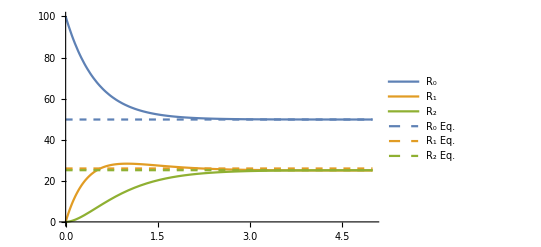

```mathematica
Show[Plot[Evaluate[{R0[t],R1[t],R2[t]}/.KPR1Sol[{kon->1,c->1,RT->100,koff->1,kf->1,δ02->5,δ21->5}]],{t,0,5},PlotLegends->{"R_0","R_1","R_2"}],
Plot[{R0KPR1[1,1,1,1,5,5,100],R1KPR1[1,1,1,1,5,5,100]+1,R2KPR1[1,1,1,1,5,5,100]},{t,0,5},PlotRange->{Automatic,{0,105}},PlotLegends->{"R_0 Eq.","R_1 Eq.","R_2 Eq."},PlotStyle->Dashed]]
```

```mathematica
expandParams={x->(kon c)/koff,g->koff/kf};
KPR1Eq=1/(1+g)x/(1+x)/.expandParams;
μN1=kp t KPR1Eq;
σ2N1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;
```

```mathematica
μN1NonEq=kp t R2KPR1[c,kon,koff,kf,δ21,δ02,RT];
```

#### Variance for N=1 Reversible KPR model

```mathematica
σ2N1NonEq=kp (1/(c ν+ⅇ^(δ02/kT) (koff+c ν))ⅇ^(δ02/kT) koff ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(2 c ⅇ^((δ02+2 δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) r0 ν (-ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((2 δ02+δ21)/kT) kf-c ⅇ^(δ21/kT) r0 ν-c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 c ⅇ^(δ02/kT+(2 δ21)/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) r0 ν (-ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((2 δ02+δ21)/kT) kf-c ⅇ^(δ21/kT) r0 ν-c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))+(c ⅇ^(δ21/kT) (kf+ⅇ^(δ02/kT) kf+koff r0) ν ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)-(2 ⅇ^((2 δ02+δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-ⅇ^(δ02/kT) kf^2-ⅇ^((δ02+δ21)/kT) kf^2-ⅇ^((δ02+δ21)/kT) kf koff r0+ⅇ^((δ02+2 δ21)/kT) kf koff r0+c ⅇ^(δ21/kT) kf r0 ν+c ⅇ^((δ02+δ21)/kT) kf r0 ν-c ⅇ^((2 δ21)/kT) koff r0^2 ν+c ⅇ^((δ02+2 δ21)/kT) koff r0^2 ν+ⅇ^((δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((δ02+2 δ21)/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 ⅇ^((2 δ02)/kT+δ21/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) (ⅇ^(δ02/kT) kf^2+ⅇ^((δ02+δ21)/kT) kf^2+ⅇ^((δ02+δ21)/kT) kf koff r0-ⅇ^((δ02+2 δ21)/kT) kf koff r0-c ⅇ^(δ21/kT) kf r0 ν-c ⅇ^((δ02+δ21)/kT) kf r0 ν+c ⅇ^((2 δ21)/kT) koff r0^2 ν-c ⅇ^((δ02+2 δ21)/kT) koff r0^2 ν+ⅇ^((δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((δ02+2 δ21)/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0) (c ν+ⅇ^(δ02/kT) (koff+c ν)))+(c (kf+ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) koff r0) ν ((c kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) kf r0 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)+(c ⅇ^(-δ02/kT) koff r0^2 t ν)/(kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-δ02/kT-δ21/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν)-(2 ⅇ^((2 δ02)/kT+(2 δ21)/kT-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-1+ⅇ^(1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))))) (ⅇ^(δ02/kT) kf^2-c ⅇ^(δ21/kT) r0 (kf+2 koff r0) ν+ⅇ^((δ02+δ21)/kT) kf (kf+2 koff r0-c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (ⅇ^((2 δ02)/kT) kf^2+ⅇ^((2 (δ02+δ21))/kT) kf^2+2 ⅇ^((2 δ02+δ21)/kT) kf^2-2 c ⅇ^((δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν-2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν-2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν+c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2+c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2+2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))+(2 ⅇ^((2 (δ02+δ21))/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))) (-ⅇ^(δ02/kT) kf^2+c ⅇ^(δ21/kT) r0 (kf+2 koff r0) ν+ⅇ^((δ02+δ21)/kT) kf (-kf-2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (-ⅇ^((2 δ02)/kT) kf^2-ⅇ^((2 (δ02+δ21))/kT) kf^2-2 ⅇ^((2 δ02+δ21)/kT) kf^2+2 c ⅇ^((δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((2 (δ02+δ21))/kT) kf r0 ν+2 c ⅇ^((2 δ02+δ21)/kT) kf r0 ν+2 c ⅇ^((δ02+2 δ21)/kT) kf r0 ν-c^2 ⅇ^((2 δ21)/kT) r0^2 ν^2-c^2 ⅇ^((2 (δ02+δ21))/kT) r0^2 ν^2-2 c^2 ⅇ^((δ02+2 δ21)/kT) r0^2 ν^2+ⅇ^((2 (δ02+δ21))/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+ⅇ^((2 δ02+δ21)/kT) kf √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+2 ⅇ^((2 (δ02+δ21))/kT) koff r0 √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((2 (δ02+δ21))/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)+c ⅇ^((δ02+2 δ21)/kT) r0 ν √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0) (c ν+ⅇ^(δ02/kT) (koff+c ν))))+kp^2 (-(c^2 ⅇ^((2 δ21)/kT) (kf+ⅇ^(δ02/kT) kf+koff r0)^2 t^2 ν^2)/((kf+ⅇ^(δ21/kT) kf+ⅇ^(δ21/kT) koff r0)^2 (c ν+ⅇ^(δ02/kT) (koff+c ν))^2)+2 ((c ⅇ^(δ21/kT) (kf+ⅇ^(δ02/kT) kf+koff r0) t^2 ν)/(2 (kf+ⅇ^(δ21/kT) (kf+koff r0)) (c ν+ⅇ^(δ02/kT) (koff+c ν)))-(2 ⅇ^((δ02+δ21)/kT) (-t-(2 ⅇ^((δ02+δ21)/kT) (-1+ⅇ^(1/2 t (-kf-ⅇ^(-δ21/kT) kf-2 koff r0-c r0 ν-c ⅇ^(-δ02/kT) r0 ν+√(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)))))/(ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))) (ⅇ^(-δ21/kT) kf^2+c ⅇ^(-δ02/kT) koff r0^2 ν-1/2 ⅇ^(-(δ02+2 δ21)/kT) (kf+ⅇ^(δ21/kT) koff r0) (-ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν-ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-(δ02+δ21)/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν-ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν)) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))+3/4 ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))^2))+(2 ⅇ^((δ02+δ21)/kT) (t+(2 ⅇ^((δ02+δ21)/kT) (-1+ⅇ^(-1/2 ⅇ^(-(δ02+δ21)/kT) t (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2))))))/(ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2))) (ⅇ^(-δ21/kT) kf^2+c ⅇ^(-δ02/kT) koff r0^2 ν-1/2 ⅇ^(-(δ02+2 δ21)/kT) (kf+ⅇ^(δ21/kT) koff r0) (-ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+c r0 ν-√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))))/((ⅇ^(δ02/kT) kf+ⅇ^((δ02+δ21)/kT) kf+2 ⅇ^((δ02+δ21)/kT) koff r0+c ⅇ^(δ21/kT) r0 ν+c ⅇ^((δ02+δ21)/kT) r0 ν+ⅇ^((δ02+δ21)/kT) √(((1+ⅇ^(-δ21/kT)) kf+c (-1-ⅇ^(-δ02/kT)) r0 ν)^2)) (kf koff r0+ⅇ^(-δ21/kT) kf koff r0+koff^2 r0^2+c kf r0 ν+c ⅇ^(-δ02/kT) kf r0 ν+c ⅇ^(-δ21/kT) kf r0 ν+c ⅇ^(-(δ02+δ21)/kT) kf r0 ν+c koff r0^2 ν+c ⅇ^(-δ02/kT) koff r0^2 ν-ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν)) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))+3/4 ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf+c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf+2 koff r0+c r0 ν+√(ⅇ^(-(2 (δ02+δ21))/kT) (ⅇ^(δ02/kT) kf-c ⅇ^(δ21/kT) r0 ν+ⅇ^((δ02+δ21)/kT) (kf-c r0 ν))^2)))^2))));
```

```mathematica
σ2N1NonEq=σ2N1NonEq/.{r0->1,ν->kon,kT->1};
```

#### Mixed Ligands for KPR 1

```mathematica
mixedLigandsKPR1eqs={
0==-(kon c1+kon c2) P0+koff1(P1a+P2a)+koff2(P1b+P2b),
0==kon c1 P0-(koff1+kf)P1a,
0==kf P1a-koff1 P2a,
0==kon c2 P0-(koff2+kf)P1b,
(*0==kf P1b-koff2 P2b*)
P0+P1a+P2a+P1b+P2b==1};
mixedKPR={P0,P1a,P2a,P1b,P2b}/.Solve[mixedLigandsKPR1eqs,{P0,P1a,P2a,P1b,P2b}][[1]]
```

{(koff1 koff2)/(koff1 koff2+c2 koff1 kon+c1 koff2 kon),(c1 koff1 koff2 kon)/((kf+koff1) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c1 kf koff2 kon)/((kf+koff1) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c2 koff1 koff2 kon)/((kf+koff2) (koff1 koff2+c2 koff1 kon+c1 koff2 kon)),(c2 kf koff1 kon)/((kf+koff2) (koff1 koff2+c2 koff1 kon+c1 koff2 kon))}

### Adaptive Sorting

Taken from Francois and Altan-Bonnet (2016), Journal of Statistical Physics
-Graphics-
To map this model to the other models we consider here, relabel ϕ→ k_f and τ→k_off^-1 (ν1→k_off)

In the non-saturated receptor regime, we use the approximation provided from the above cited paper:

```mathematica
ASResponse[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09,b->0.04,γ->1.2*10^-6,St->600000,α->0.05,β->25},
tend_:300]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,δtest=10,sol},
ASeqs={
S'[t]==α(C1[t]+D1[t])(St-S[t])-β S[t],
C0'[t]==κ(L1-(C0[t]+C1[t]+C2[t]))(R-(C0[t]+C1[t]+C2[t]+D0[t]+D1[t]+D2[t]))+(b+γ S[t])C1[t]-(ϕ+ν1)C0[t],
C1'[t]==ϕ C0[t]+(b+γ S[t])C2[t]-(ϕ+b+γ S[t]+ν1)C1[t],
C2'[t]==ϕ C1[t]-(b+γ S[t]+ν1)C2[t],
D0'[t]==κ(L2-(D0[t]+D1[t]+D2[t]))(R-(C0[t]+C1[t]+C2[t]+D0[t]+D1[t]+D2[t]))+(b+γ S[t])D1[t]-(ϕ+ν2)D0[t],
D1'[t]==ϕ D0[t]+(b+γ S[t])D2[t]-(ϕ+b+γ S[t]+ν2)D1[t],
D2'[t]==ϕ D1[t]-(b+γ S[t]+ν2)D2[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,D0[0]==0,D1[0]==0,D2[0]==0};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,C2,{t,1,tend}];
(C2[tend]/.sol)[[1]]
]
```

```mathematica
0.09/10^-4
```

900.

```mathematica
AS5[c1_,c2_,kofftest_:1,
params_:{R->30000,kon->10^-4,kf->0.09,b->0.04,γ->1.2*10^-6,St->600000,α->0.05,β->25},
tend_:300,δtest_:10]:=Module[{ASeqs,p,sub,L1=c1,L2=c2,sol},
ASeqs={
S'[t]==α(C1[t]+D1[t])(St-S[t])-β S[t],
C0'[t]==κ(L1-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]))(R-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]+D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))+(b+γ S[t])C1[t]-(ϕ+ν1)C0[t],
C1'[t]==ϕ C0[t]+(b+γ S[t])C2[t]-(ϕ+b+γ S[t]+ν1)C1[t],
C2'[t]==ϕ C1[t]+(b+γ S[t])C3[t]-(ϕ+b+γ S[t]+ν1)C2[t],
C3'[t]==ϕ C2[t]+(b+γ S[t])C4[t]-(ϕ+b+γ S[t]+ν1)C3[t],
C4'[t]==ϕ C3[t]+(b+γ S[t])C5[t]-(ϕ+b+γ S[t]+ν1)C4[t],
C5'[t]==ϕ C4[t]-(b+γ S[t]+ν1)C5[t],
D0'[t]==κ(L2-(D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))(R-(C0[t]+C1[t]+C2[t]+C3[t]+C4[t]+C5[t]+D0[t]+D1[t]+D2[t]+D3[t]+D4[t]+D5[t]))+(b+γ S[t])D1[t]-(ϕ+ν2)D0[t],
D1'[t]==ϕ D0[t]+(b+γ S[t])D2[t]-(ϕ+b+γ S[t]+ν2)D1[t],
D2'[t]==ϕ D1[t]+(b+γ S[t])D3[t]-(ϕ+b+γ S[t]+ν2)D2[t],
D3'[t]==ϕ D2[t]+(b+γ S[t])D4[t]-(ϕ+b+γ S[t]+ν2)D3[t],
D4'[t]==ϕ D3[t]+(b+γ S[t])D5[t]-(ϕ+b+γ S[t]+ν2)D4[t],
D5'[t]==ϕ D4[t]-(b+γ S[t]+ν2)D5[t],
S[0]==0,C0[0]==0,C1[0]==0,C2[0]==0,C3[0]==0,C4[0]==0,C5[0]==0,D0[0]==0,D1[0]==0,D2[0]==0,D3[0]==0,D4[0]==0,D5[0]==0};
p=Join[params,{koff->kofftest,δ->δtest}];
sub={ϕ->kf,ν1->koff,ν2->δ koff,κ->kon};
ASeqs=Evaluate[ASeqs/.sub/.p];
sol=NDSolve[ASeqs,{C5,D5},{t,1,tend}];
(C5[tend]+D5[tend]/.sol)[[1]]
]
```

## Figures

### Specificity Figure

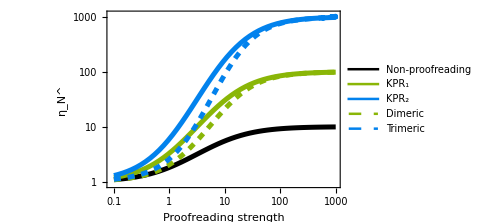

```mathematica
fig2params={Rt->10^0,c->10^0,kon->1,kf->10^0};

Fig2A=LogLogPlot[{
Evaluate[Evaluate[η0/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[Evaluate[η1/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[Evaluate[η2/.{koff->g kf}]/.fig2params/.δ->0.1],
Evaluate[HomoDimer[c,Rt,δ koff/kon ,δ (2koff)/kf ]/HomoDimer[c,Rt,koff/kon,(2koff)/kf]/.{koff->g kf}/.fig2params/.δ->0.1],
Evaluate[Tri[c,Rt,δ koff/kon ,δ (2koff)/kf,δ (3koff)/kf ]/Tri[c,Rt,koff/kon,(2koff)/kf,(3koff)/kf]/.{koff->g kf}/.fig2params/.δ->0.1]},
{g,10^-1,10^3},
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"Proofreading strength","η_N^"},PlotLegends->{"Non-proofreading","KPR_1","KPR_2","Dimeric","Trimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},PlotStyle->Join[Table[{clist[[i]],Thickness[0.01]},{i,1,3}],Table[{clist[[i]],Thickness[0.01],Dashed},{i,2,3}]],
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,0,3}],None},{Table[{10^i,Superscript[10,i]},{i,-2,4}],None}},TicksStyle->Black,PlotRange->{{0.9*10^-1,1*10^3},{0.9,1.1*10^3}}]
```

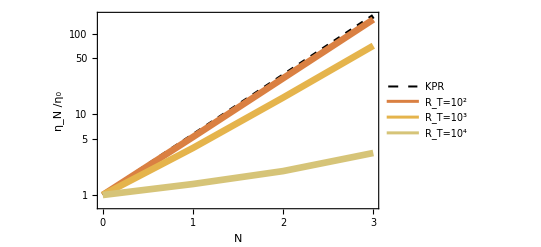

```mathematica
clist2=Table[ColorData["BeachColors",i/(5-1)],{i,0,5-1}];

KOFF=10;
KON=1;
KF=10^0;
RT=10^0;
δK=0.1;
CTEST=1;
testparams={kf->KF,koff->KOFF,kon->KON,c->CTEST,δ->0.1,Rt->RT};


ηREF=η0/.testparams;
KPRscaling={{0,η0/η0},{1,η1/η0},{2,η2/η0},{3,η3/η0}}/.testparams;
MultimerScaling={{0,1},{1,1/ηREF HomoDimer[CTEST,RT,δK KOFF/KON,δK(2KOFF)/KF]/HomoDimer[CTEST,RT,KOFF/KON,(2KOFF)/KF]},{2,1/ηREF Tri[CTEST,RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF]/Tri[CTEST,RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF]},{3,1/ηREF TetAct[CTEST,RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF,δK(4KOFF)/KF]/TetAct[CTEST,RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF,(4KOFF)/KF]}};

MultimerScalingReducedRt={{0,1},{1,1/ηREF HomoDimer[CTEST,0.1RT,δK KOFF/KON,δK(2KOFF)/KF]/HomoDimer[CTEST,0.1RT,KOFF/KON,(2KOFF)/KF]},{2,1/ηREF Tri[CTEST,0.1RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF]/Tri[CTEST,0.1RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF]},{3,1/ηREF TetAct[CTEST,0.1RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF,δK(4KOFF)/KF]/TetAct[CTEST,0.1RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF,(4KOFF)/KF]}};
MultimerScalingIncreasedRt={{0,1},{1,1/ηREF HomoDimer[CTEST,10RT,δK KOFF/KON,δK(2KOFF)/KF]/HomoDimer[CTEST,10RT,KOFF/KON,(2KOFF)/KF]},{2,1/ηREF Tri[CTEST,10RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF]/Tri[CTEST,10RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF]},{3,1/ηREF TetAct[CTEST,10RT,δK KOFF/KON,δK(2KOFF)/KF,δK(3KOFF)/KF,δK(4KOFF)/KF]/TetAct[CTEST,10RT,KOFF/KON,(2KOFF)/KF,(3KOFF)/KF,(4KOFF)/KF]}};


Fig2B=ListLogPlot[{KPRscaling,MultimerScalingReducedRt,MultimerScaling,MultimerScalingIncreasedRt},
PlotStyle->Join[{{Black,Thickness[0.008],Dashed}},Table[{clist2[[i]],Thickness[0.012]},{i,1,3}]],LabelStyle-> {Black,FontSize->16},
Joined->True,PlotLegends->{"KPR","R_T=10^2","R_T=10^3","R_T=10^4"},Frame->{{True,False},{True,False}},FrameLabel->{"N","η_N /η_0"},FrameStyle->Black,FrameTicks->{{0,1,2,3},Automatic}]
```

### Heteromultimer Figure

10

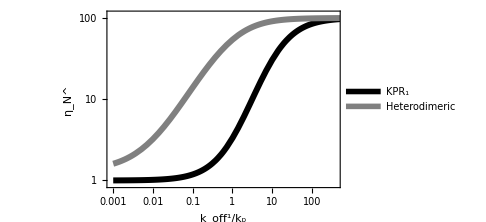

```mathematica
(*
cellSA=4π 10^3;
{koff1->gf,kon->2*10^5,koff2->0.015,koff4->0.29*4π*0.094*cellSA*gf,kf->4π*0.094*cellSA};
*)
IFNαParams={Rt->10^4,Δ->0,IFN->10^-3,ζ->0.1,koff1->gf,kon->1,koff2->2,koff4->0.5*gf,kf->10^-3};
kf Rt/.IFNαParams
FigHetB=LogLogPlot[{

((kf+koff) (koff+c kon))/((kf+koff ζ) (c kon+koff ζ))/.{c->10^-3,kon->1,kf->10^-3,ζ->0.1,koff->10^-3 gf},
η2Het/.IFNαParams
},{gf,0.001,10^4},
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"k_off^1/k_p","η_N^"},PlotLegends->{"KPR_1","Heterodimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},
PlotStyle->{{Black,Thickness[0.012]},{Gray,Thickness[0.012]}},
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,0,3}],None},{Table[{10^i,Superscript[10,i]},{i,-5,4}],None}},TicksStyle->Black,PlotRange->{{0.9*10^-3,4*10^2},{0.9,1.1*10^2}}]
```

```mathematica
testparams1={R1T->10000/3,R2T->10000/3,R3T->10000/3,kon->1,kf->1/10000,koff1->2,koff2->4,koff3->8,koff4->16,θ->0.5};
testparams2={R1T->10000/3,R2T->10000/3,R3T->10000/3,kon->1,kf->1/10000,koff1->0.1*2,koff2->0.1*4,koff3->0.1*8,koff4->0.1*16,θ->0.5};

1/(ηREF/.IFNαParams)μ3Het[Join[testparams2,{c->0.02}],100000000]/μ3Het[Join[testparams1,{c->0.1}],100000000]
```

19.0663

```mathematica
testparams3={R1T->10000/4,R2T->10000/4,R3T->10000/4,R4T->10000/4,kon->1,kf->1/10000,koff1->2,koff2->4,koff3->8,koff4->16,θ->0.5};
testparams4={R1T->10000/4,R2T->10000/4,R3T->10000/4,R4T->10000/4,kon->1,kf->1/10000,koff1->0.1*2,koff2->0.1*4,koff3->0.1*8,koff4->0.1*16,θ->0.5};
1/(ηREF/.testparams2)μ4Het[Join[testparams4,{c->0.02}],100000000]/μ4Het[Join[testparams3,{c->0.02}],100000000]
```

807.822

```mathematica
testparams5={R1T->10000/2,R2T->10000/2,kon->1,kf->1/10000,koff1->2,koff2->4,(*koff3->8,koff4->16,*)θ->0.5};
testparams6={R1T->10000/2,R2T->10000/2,kon->1,kf->1/10000,koff1->0.1*2,koff2->0.1*4,(*koff3->0.1*8,koff4->0.1*16,*)θ->0.5};
1/ηREF μ2HetNonEqAlt[Join[testparams6,{δ->0,c->0.02}]]/μ2HetNonEqAlt[Join[testparams5,{δ->0,c->0.02}]]
```

11.4743

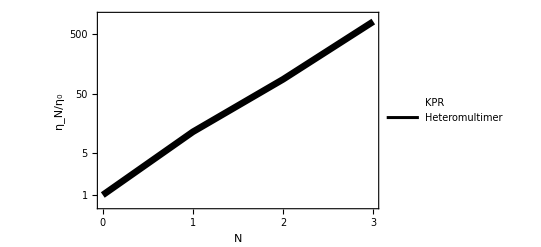

```mathematica
KOFF=1;
KON=1;
KF=10^-4;
RT=10^3;
δK=0.1;
CTEST=0.01;
ζTEST=0.1;
KPRparams={kf->KF,koff->KOFF,kon->KON,c->CTEST,IFN->CTEST,δ->ζTEST,ζ->ζTEST,Rt->RT,Δ->0,θ ->θTEST};

ηREF=η0/.δ->0.1/.koff->koff1/.testparams2/.{c->0.02};
KPRscaling={{0,η0/η0},{1,η1/η0},{2,η2/η0},{3,η3/η0}}/.KPRparams;
HeteromultimerScaling={
{0,1},
{1,1/ηREF μ2HetNonEqAlt[Join[testparams6,{δ->0,c->0.02}],100000000]/μ2HetNonEqAlt[Join[testparams5,{δ->0,c->0.02}],100000000]},
{2,1/ηREF μ3Het[Join[testparams2,{c->0.02}],100000000]/μ3Het[Join[testparams1,{c->0.02}],100000000]},
{3,1/ηREF μ4Het[Join[testparams4,{c->0.02}],100000000]/μ4Het[Join[testparams3,{c->0.02}],100000000]}};
FigHetC=ListLogPlot[{KPRscaling,HeteromultimerScaling},
PlotStyle->{{White,Thickness[0.008],Dashed},{Black,Thickness[0.012]}},
LabelStyle-> {Black,FontSize->16},
Joined->True,PlotLegends->{"KPR","Heteromultimer"},Frame->{{True,False},{True,False}},FrameLabel->{"N","η_N/η_0"},FrameStyle->Black,FrameTicks->{{0,1,2,3},{1,5,50,500}}]
```

### Non-equilibrium energy comparison

```mathematica
μ2HetNonEqLikeKPR[params_,tend_:300]:=Module[{eqs,sol},
eqs={
D[R1f[t],t]==-kon c R1f[t]-kf B2[t] R1f[t]+koff1 B1[t]+koff1 θ T[t],
D[R2f[t],t]==-kon c R2f[t]-kf B1[t] R2f[t]+E^δ koff2 B2[t]+E^δ koff2 θ T[t],

D[B1[t],t]==kon c R1f[t]-koff1 B1[t]-kf B1[t]R2f[t]+E^δ koff2 θ T[t],
D[B2[t],t]==kon c R2f[t]-E^δ koff2 B2[t]-kf B2[t]R1f[t]+koff1 θ T[t],

D[T[t],t]==kf B2[t] R1f[t]+kf B1[t] R2f[t]-θ T[t](koff1+E^δ koff2),

R1f[0]==R1T,R2f[0]==R2T,B1[0]==0,B2[0]==0,T[0]==0}/.params;

sol=NDSolve[eqs,T,{t,0,tend}];
(T[tend]/.sol)[[1]]
];
```

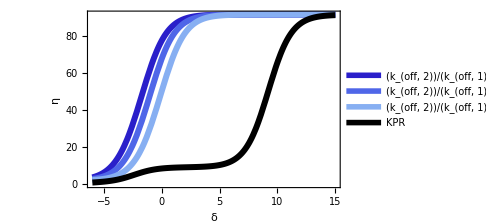

```mathematica
KOFF=1;
KON=1;
KF=10^-4;
RT=0.5*10^4;
δK=0.1;
CTEST=0.01;
θTEST=0.5;
KOFF=1;
Figure7=Plot[{μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->δK KOFF,koff2->δK 10KOFF,θ->0.5,δ->δTEST,c->CTEST}]/μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->KOFF,koff2->10KOFF,θ->0.5,δ->δTEST,c->CTEST}],
μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->δK KOFF,koff2->δK 5KOFF,θ->0.5,δ->δTEST,c->CTEST}]/μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->KOFF,koff2->5KOFF,θ->0.5,δ->δTEST,c->CTEST}],
μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->δK KOFF,koff2->δK 2KOFF,θ->0.5,δ->δTEST,c->CTEST}]/μ2HetNonEqLikeKPR[{R1T->RT,R2T->RT,kon->1,kf->KF,koff1->KOFF,koff2->2KOFF,θ->0.5,δ->δTEST,c->CTEST}],
R2KPR1[CTEST,KON,δK KOFF,KF,δTEST,δTEST,RT]/R2KPR1[CTEST,KON,KOFF,KF,δTEST,δTEST,RT]},
{δTEST,-6,15},
PlotStyle->{{bigrad[[1]],Thickness[0.012]},{bigrad[[2]],Thickness[0.012]},{bigrad[[3]],Thickness[0.012]},{Black,Thickness[0.012]}},
LabelStyle-> {Black,FontSize->16},
PlotLegends->{"(k_(off, 2))/(k_(off, 1))=10","(k_(off, 2))/(k_(off, 1))=5","(k_(off, 2))/(k_(off, 1))=2","KPR"},Frame->{{True,False},{True,False}},FrameLabel->{"δ","η"},FrameStyle->Black,ImageSize->Medium]
```

### Free Energy Landscapes Figure

S=k_B Log[Ω]  and Ω=Σ_i(A/a_0)^R_i/(R_i!) in the dilute limit.
Using Stirling’s approximation, Log(x!)=x(Log[x]-1), this becomes

S=k_B Σ_i(R_i Log[A/a_0]-R_i Log[R_i]+R_i)
S=-k_BΣ_i(R_i Log[a_0 R_i/A]-R_i)

```mathematica
DimerChemEq={kon c R0==koff R1,
		      kf R0 R1==koff R2};
DimerF=ϵ1 R1 A+ϵ2 R2 A-μ (R1+R2)A-kT (R1 Log[R1/A a0])
```

A R1 ϵ1+A R2 ϵ2-A (R1+R2) μ-kT R1 Log[(a0 R1)/A]

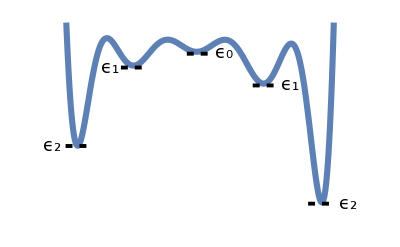

```mathematica
welldepths=Join[
Table[{-Ns,-Log[(0.2koff)/kon((0.2koff)/kf)^Ns 1/((Ns+1)!)]}/.{kon->1,koff->1,kf->0.01},{Ns,3,1,-1}],
Table[{Ns,-Log[koff/kon(koff/kf)^Ns 1/((Ns+1)!)]}/.{kon->1,koff->1,kf->0.01},{Ns,0,3}]
];
wellheights=Table[{i,welldepths[[i+3.5,2]]+2},{i,-2.5,2.5}];
landscape1=Riffle[welldepths,wellheights];
landscape1[[6,2]]=0.9landscape1[[8,2]];


Fig3A=Plot[{
Interpolation[landscape1,InterpolationOrder->12][Rx],
Piecewise[{{-0.4,Abs[Rx]<0.25}},None],
Piecewise[{{-5.9,Abs[Rx-1.25]<0.25}},None],
Piecewise[{{-2.8,Abs[Rx+1.25]<0.25}},None],
Piecewise[{{-26.4,Abs[Rx-2.3]<0.25}},None],
Piecewise[{{-16.4,Abs[Rx+2.3]<0.25}},None]},
{Rx,-2.6,2.6},

Axes->False,
PlotStyle->Join[{{cmap[[1]],Thickness[0.011]}},Table[{Black,Dashed,Thickness[0.007]},{i,1,5}]],
PlotRange->{{-3.1,3.1},{-30,5}},

Epilog->{
Text[Style["ϵ_0",FontSize->18],{0.45,-0.25}],
Text[Style["ϵ_1",FontSize->18],{1.7,-5.9}],
Text[Style["ϵ_2",FontSize->18],{2.8,-26.4}],
Text[Style["ϵ_1",FontSize->18],{-1.7,-2.8}],
Text[Style["ϵ_2",FontSize->18],{-2.8,-16.4}]}]
```

```mathematica
(* Figure 3B was made in Inkscape. *)
```

### SNR Figure

```mathematica
CellRadius=6; (* μm *)
CellSA=4π CellRadius^2//N
CellSA=500
ka4α=4π*0.094;
CellSA*ka4α
```

452.389

500

590.619

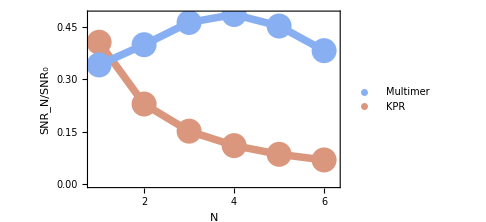

```mathematica
(*Type I IFN and KPR parameters*)
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=1;
CPARAM=10^-2;
RTPARAM=5*10^2;
TPARAM=100;
KFPARAM=1/CellSA;
KPRkfPARAM=0.1(Ns+1);
MultimerParams={kon->10^0,koff->10KOFF,c->CPARAM,kf->KFPARAM,kp->1,t->TPARAM};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->TPARAM,kf->KPRkfPARAM};
NSMAX=6;

SNRvN=
Table[{Ns,MultSNRGeneral[MultGeneral[1,CPARAM,KOFF,KFPARAM,(Ns+1)RTPARAM,Ns],MultGeneralR0[1,CPARAM,KOFF,KFPARAM,(Ns+1)RTPARAM,Ns],1,TPARAM,Ns]/(√Rt μ0/(√Σ0)/.Rt->(Ns+1)RTPARAM)},{Ns,1,NSMAX}]/.MultimerParams//N;
KprSnrExpression=(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.KPRparams;
SNRkprvN=Table[{Ns,KprSnrExpression },{Ns,1,NSMAX}]/.KPRparams//N;
Fig4Ca=
Legended[
Show[
ListPlot[{SNRkprvN,SNRvN},Joined->True,PlotStyle->{{bigrad[[7]],Thickness[0.015]},{bigrad[[3]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,NSMAX}],Automatic},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{0.85,NSMAX+0.25},{Automatic,All}}],
ListPlot[{SNRkprvN,SNRvN},PlotStyle->{{bigrad[[7]],PointSize[0.05]},{bigrad[[3]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

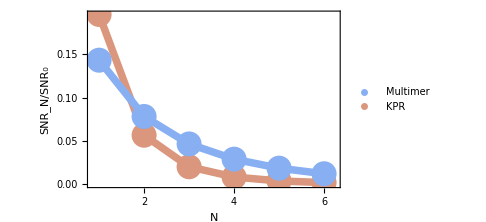

```mathematica
(*Strong proofreading*)
gxTicks={{Table[{i,Superscript[10,i]},{i,-2,2}],None},{Table[{i,Superscript[10,i]},{i,-3,3,2}],None}};
KOFF=5;
CPARAM=10^-2;
RTPARAM=5*10^2;
KFPARAM=1/500;
KPRkfPARAM=0.1(Ns+1);
MultimerParams={kon->10^0,koff->10KOFF,c->CPARAM,kf->KFPARAM,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100,kf->KPRkfPARAM};
NSMAX=6;

SNRvN=
Table[{Ns,MultSNRGeneral[MultGeneral[1,CPARAM,KOFF,KFPARAM,(Ns+1)RTPARAM,Ns],MultGeneralR0[1,CPARAM,KOFF,KFPARAM,(Ns+1)RTPARAM,Ns],1,100,Ns]/(√Rt μ0/(√Σ0)/.Rt->(Ns+1)RTPARAM)},{Ns,1,NSMAX}]/.MultimerParams//N;
KprSnrExpression=(μN/(√ΣN))/(μ0/(√Σ0))/.expandParams/.KPRparams;
SNRkprvN=Table[{Ns,KprSnrExpression },{Ns,1,NSMAX}]/.KPRparams//N;
Fig4Cb=
Legended[
Show[
ListPlot[{SNRkprvN,SNRvN},Joined->True,PlotStyle->{{bigrad[[7]],Thickness[0.015]},{bigrad[[3]],Thickness[0.015]}},ImageSize->Medium,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N/SNR_0"},FrameTicks->{Table[i,{i,0,NSMAX}],Automatic},TicksStyle->{Black,FontSize->24},LabelStyle->{Black,FontSize->24},PlotRange->{{0.85,NSMAX+0.25},{Automatic,All}}],
ListPlot[{SNRkprvN,SNRvN},PlotStyle->{{bigrad[[7]],PointSize[0.05]},{bigrad[[3]],PointSize[0.05]}},ImageSize->Medium]
],
PointLegend[{bigrad[[3]],bigrad[[7]]},{"Multimer","KPR"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

### Absolute Discrimination Figure

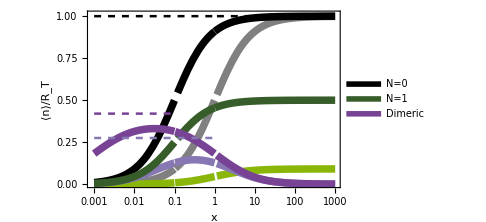

```mathematica
ClearAll[CTEST];
testParams={kon->1,kp->1,t->100,c->CTEST ,koff->1,kf->0.1,Rt->10,δ->0.1};
μ2HetExprsn=kp t μ2Het/.{IFN->c,koff1->koff,koff4-> 0.5koff,koff2->0.1koff,Δ->0};
clist={categoricalcmap[[4]],ColorData[8,"ColorList"][[7]],cmap[[5]],categoricalcmap[[8]]};
plotoptions={
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"x","⟨n⟩/R_T"},
PlotLegends->{None,None,None,"N=0","N=1","Dimeric"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},

PlotStyle->{
{Gray,Thickness[0.015]},
{clist[[1]],Thickness[0.015]},
{clist[[3]],Thickness[0.015]},
{Black,Thickness[0.015]},
{clist[[2]],Thickness[0.015]},
{clist[[4]],Thickness[0.015]},
{Black,Dashed,Thickness[0.005]},
{clist[[4]],Dashed,Thickness[0.005]},
{clist[[3]],Dashed,Thickness[0.005]}},

FrameTicks->{{Automatic,None},{Table[{10^i,Superscript[10,i]},{i,-3,3}],None}},TicksStyle->Black,PlotRange->{{0.0009,1010},{0.000000001,1.01}}};
expression=#/.testParams&/@{μ0/(kp t),μ1/(kp t),μ2HetExprsn/(kp t Rt),Evaluate[μ0/(kp t)/.koff->δ koff],Evaluate[μ1/(kp t)/.koff->δ koff],Evaluate[μ2HetExprsn/(kp t Rt)/.koff->δ koff]};
expression=Join[Evaluate@expression,{1,0.42*HeavisideTheta[0.1-CTEST],0.275*HeavisideTheta[1-CTEST]}];

Fig5A=LogLinearPlot[Evaluate@expression,{CTEST,0.001,1000},Evaluate@plotoptions]
```

```mathematica
AScontourplot=ContourPlot[10^3 AS5[10^CTEST,0,10^KTEST],{KTEST,-3,1},{CTEST,-5,7}];
points=Cases[Normal@AScontourplot,Line[pts_]->pts,Infinity];
```

```mathematica
p1={kon->10^0,kp->1,t->300,Nx->30,kf->1};
p2={kon->10^0,kp->1,t->300,Ny->3000,kf->0.01,Rt->100};

c0=Solve[μ0== Nx,c][[1]];
c1=Solve[μ1== Nx,c][[1]];
c2=Solve[μ2== Nx,c][[1]];
c5=Solve[Evaluate[μN/.Ns->5]== Nx,c][[1]];
cDim=Solve[μDi==Ny,c];

ls=c/.{c0/.p1,c1/.p1,c2/.p1,c5/.p1,cDim/.p2};
```

```mathematica
μ2HetContourPlot=ContourPlot[(300μ2Het/.{IFN->10^CTEST,Δ->0,Rt->2Rt,koff1->10^KTEST,koff2->10^-4,koff4->10^KTEST})/.p2,{KTEST,-3,2},{CTEST,-8,3},PlotRange->All,Contours->{6000}];
μ2Hetpoints=Cases[Normal@μ2HetContourPlot,Line[pts_]->pts,Infinity][[1]];
```

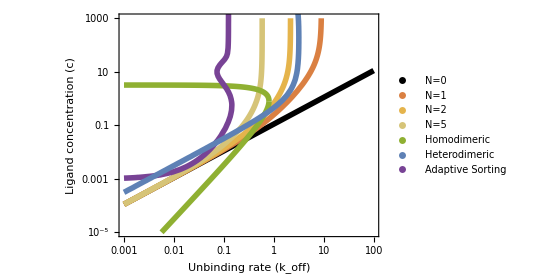

```mathematica
KPRcolors=Table[ColorData["BeachColors",i/(5-1)],{i,0,5-1}];
AScolors=categoricalcmap[[8]];
Dimercolors=ColorData[97,"ColorList"][[1]];

Fig5B=Legended[
Show[
LogLogPlot[ls,{koff,10^-3,10^2},AspectRatio->0.7,PlotRange->{{0.001,100},{10^-5,10^3}},PlotStyle->Join[{{Black,Thickness[0.01]}},Table[{KPRcolors[[i]],Thickness[0.01]},{i,1,3}],{{cmap[[3]],Thickness[0.01]},{cmap[[3]],Thickness[0.01]}}],
Frame->{{True,False},{True,False}},FrameLabel->{"Unbinding rate (k_off)","Ligand concentration (c)"},TicksStyle->Black,LabelStyle->{Black,FontSize->18},FrameTicks->{{Table[{10^i,Superscript[10,i-4]},{i,-6,6,2}],None},{Table[{10^i,Superscript[10,i]},{i,-3,4}],None}}],

ListLogLogPlot[Evaluate[{10^#[[1]],1/900 10^#[[2]](*normalize by Subscript[k, p]/Subscript[k, on]*)}&/@points[[6]]],AspectRatio->0.7,Joined->True,PlotStyle->{AScolors,Thickness[0.01]}],
ListLogLogPlot[Evaluate[{10^#[[1]],10^4*10^#[[2]]}&/@μ2Hetpoints],AspectRatio->0.7,Joined->True,PlotStyle->{Dimercolors,Thickness[0.01]}]
],
PointLegend[Join[{{Black,Thickness[0.01]}},Table[KPRcolors[[i]],{i,1,3}],{cmap[[3]],Dimercolors,AScolors}],
{"N=0","N=1","N=2","N=5","Homodimeric","Heterodimeric","Adaptive Sorting"},LegendMarkerSize->25,LegendLayout->{"Column",2}]
]
```

### Figure S1(Gillespie simulations to validate expression of dimeric variance)

```mathematica
simparams={NA->6.022*10^23,volEC->10^-5,kon->3.321*10^-14,koff->1,kf->3.623*10^-4,kr->1,kp->10^-6,Rt->4000,t->10^4};
```

```mathematica
dat=Import["Gillespie-validation.csv","Data"];
doses=Table[dat[[i,1]],{i,2,Length[dat]}];
meanN=Table[dat[[i,2]],{i,2,Length[dat]}];
sigN=Table[dat[[i,3]],{i,2,Length[dat]}];
meanR=Table[dat[[i,4]],{i,2,Length[dat]}];
sigR=Table[dat[[i,5]],{i,2,Length[dat]}];
meanNtheory=Table[dat[[i,6]],{i,2,Length[dat]}];
sigNtheory=Table[dat[[i,7]],{i,2,Length[dat]}];
meanRtheory=Table[dat[[i,8]],{i,2,Length[dat]}];
sigRtheory=Table[dat[[i,9]],{i,2,Length[dat]}];
```

```mathematica
FigS1=Row[{
ListLogLinearPlot[
{Table[{doses[[i]],meanN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanN[[i]]+sigN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanN[[i]]-sigN[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]+sigNtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanNtheory[[i]]-sigNtheory[[i]]},{i,1,Length[doses]}]
},
Joined->True,PlotStyle->{{cmap[[1]],Thickness[0.01]},None,None,{Black,Dashed,Thickness[0.01]},{Black,Dashed,Thickness[0.005]},{Black,Dashed,Thickness[0.005]}},
Filling->{1->{2},1->{3}},
PlotRange->All,PlotLabel->"Receptor Output, n",FrameLabel->{"c (pM)","n"},
Frame->{{True,False},{True,False}},LabelStyle->{Black,FontSize->16},TicksStyle->Black,ImageSize->Medium],

ListLogLogPlot[{
Table[{doses[[i]],meanR[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanR[[i]]+sigR[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],Max[10^-8,meanR[[i]]-sigR[[i]]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanRtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],meanRtheory[[i]]+sigRtheory[[i]]},{i,1,Length[doses]}],
Table[{doses[[i]],Max[10^-8,meanRtheory[[i]]-sigRtheory[[i]]]},{i,1,Length[doses]}]},
Joined->True,PlotStyle->{{cmap[[2]],Thickness[0.01]},None,None,{Black,Dashed,Thickness[0.01]},{Black,Dashed,Thickness[0.005]},{Black,Dashed,Thickness[0.005]}},
Filling->{1->{2},1->{3}},
PlotRange->{All,{10^-4,Automatic}},PlotLabel->"Receptor Signal State Occupancy, R_2",FrameLabel->{"c (pM)","R_2"},
Frame->{{True,False},{True,False}},LabelStyle->{Black,FontSize->16},TicksStyle->Black,ImageSize->Medium]
}]
```

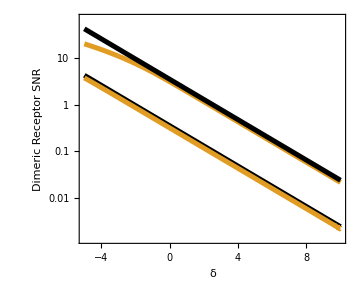

```mathematica
p1={kon->10^0,kp->1,t->100,Nx->30,kf->1,RT->100};
p2={kon->10^0,kp->1,t->100,Ny->3000,kf->0.01,RT->100};
FigS1C=LogPlot[{
SNRDimerNonEq/.p1/.{c->10^-3,koff->1,δ21->δTEST},3.5(E)^(-δTEST/2),
0.35(E)^(-δTEST/2),SNRDimerNonEq/.p2/.{c->10^-3,koff->1,δ21->δTEST}},{δTEST,-5,10},
Frame->{{True,False},{True,False}},FrameLabel->{"δ","Dimeric Receptor SNR"},FrameStyle->Black,LabelStyle->{Black,FontSize->24},ImageSize->Medium,AspectRatio->0.8,FrameTicks->{Automatic,{1000,100,10,1,0.1,0.01,0.001}},PlotStyle->{{cmap[[2]],Thickness[0.01]},{Black,Thickness[0.01]},{Black,Thickness[0.01]},{cmap[[2]],Thickness[0.01]}}]
```

### Figure S2 (More details on the reversible KPR model)

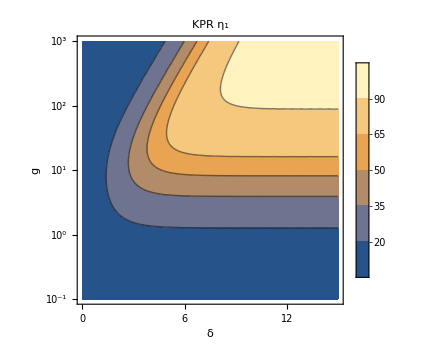

```mathematica
FigEntropyB=ContourPlot[R2KPR1[c,kon,ζ koff,kf,δ21,δ02,RT]/R2KPR1[c,kon,koff,kf,δ21,δ02,RT]/.{kon->1,c->0.001,koff->1,ζ->0.1,RT->500,δ21->δ,δ02->δ}/.{δ->δtest,kf->10^-gtest},{δtest,0,15},{gtest,-1,3},
FrameLabel->{"δ","g"},PlotLegends->Automatic,PlotLabel->"KPR η_1",LabelStyle->{Black,FontSize->24},TicksStyle->{Black,FontSize->24},ImageSize->Medium,FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Table[i,{i,0,15,3}],None}},Contours->{20,35,50,65,90}]
```

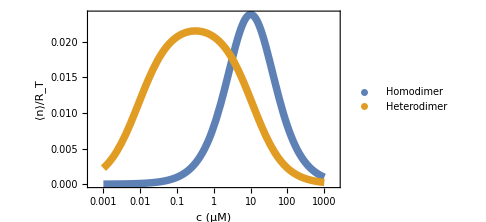

```mathematica
exp1=μDi/.{koff->koff1,c->10^-6 c};
exp2=kp t μ2Het/.{IFN->10^-6 c,koff4->koff1,Δ->0};
lines=Evaluate@{exp1/(kp t Rt/2),exp2/(kp t Rt)}/.{kon->10^5,kf->0.1,koff1->1,koff2->0.001,Rt->1,kp->1,t->100};
plotoptions={
Frame->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{"c (μM)","⟨n⟩/R_T"},
ImageSize->Medium,LabelStyle-> {Black,FontSize->16},

PlotStyle->Thickness[0.015],
FrameTicks->{{Automatic,None},{Table[{10^i,Superscript[10,i]},{i,-3,3}],None}},TicksStyle->Black};

FigS2G=Legended[
LogLinearPlot[lines,{c,10^-3,10^3},Evaluate@plotoptions],
PointLegend[{cmap[[1]],cmap[[2]]},{"Homodimer","Heterodimer"},LegendFunction->"Frame",LegendMarkerSize->30]
]
```

### Figure S3 (Other parameter regimes for SNR scaling)

```mathematica
gxTicks={{Table[{i+0.5,i},{i,1,NSMAX}],None},{Table[{i+1.5,Superscript[10,i]},{i,0,4}],None}};
KOFF=5;
CPARAM=10^-2;
RTPARAM=5*10^2;
KFPARAM=1/500;
KPRkfPARAM=0.1(Ns+1);
MultimerParams={kon->10^0,koff->10KOFF,c->CPARAM,kf->KFPARAM,kp->1,t->100};
KPRparams={kon->1,koff->KOFF,c->CPARAM,kp->1,t->100,kf->KPRkfPARAM};
NSMAX=6;
```

```mathematica
multSNRtable1=Table[Log10@(MultSNRGeneral[MultGeneral[1,CPARAM,KOFF,KFPARAM,(Ns+1)10^RTexponent,Ns],MultGeneralR0[1,CPARAM,KOFF,KFPARAM,(Ns+1)10^RTexponent,Ns],1,100,Ns]/(√Rt μ0/(√Σ0)/.Rt->(Ns+1)10^RTexponent)),{Ns,1,NSMAX},{RTexponent,0,4}]/.MultimerParams//N;
```

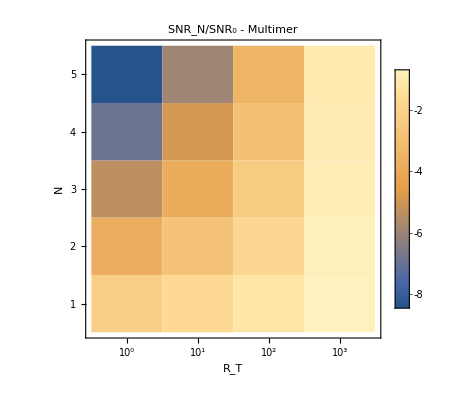

```mathematica
FigureS3=ListDensityPlot[multSNRtable1,Mesh->None,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"R_T","N"},LabelStyle->{Black,FontSize->16},PlotLabel->"SNR_N/SNR_0 - Multimer",FrameTicks->gxTicks]
```

### Figure S4 (Antagonism)

```mathematica
(*Close notebook and reopen. Run Setup *ONLY* and then run this block to make Figure S4.*)
```

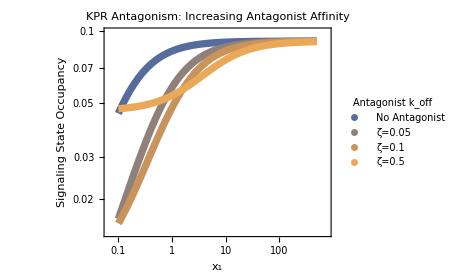

```mathematica
p={kon->1,koff1->0.1,kf->0.01};
pops={PlotStyle->Evaluate[{Thickness[0.015],#}&/@contourcmap],
Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},AspectRatio->0.8,ImageSize->350,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}};
leg=PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","ζ=0.05","ζ=0.1","ζ=0.5"},LegendMarkerSize->25,LegendLabel->"Antagonist k_off",LabelStyle->{Directive[FontSize->20]}];

μmixedKPR=mixedKPR[[3]]+mixedKPR[[5]];

FigS4A=Legended[
LogLogPlot[{μmixedKPR/.p/.{c2->0,koff2->2},
μmixedKPR/.p/.{c2->10,koff2->2},
μmixedKPR/.p/.{c2->10,koff2->1},
μmixedKPR/.p/.{c2->10,koff2->0.2}},{c1,0.1,500},PlotLabel->"KPR Antagonism:\nIncreasing Antagonist Affinity",Evaluate@pops],
leg]
```

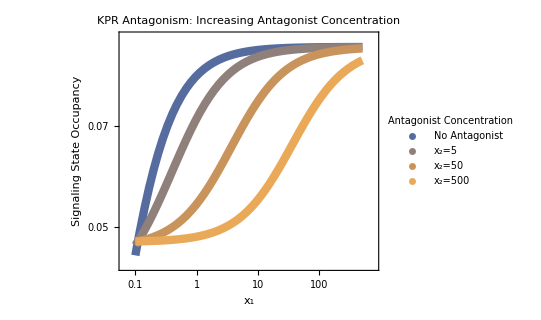

```mathematica
p={kon->1,koff1->0.1,kf->0.01};
pops={PlotStyle->Evaluate[{Thickness[0.015],#}&/@contourcmap],
Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}};
leg=PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","x_2=5","x_2=50","x_2=500"},LegendMarkerSize->25,LegendLabel->"Antagonist Concentration",LabelStyle->{Directive[FontSize->20]}];

μmixedKPR=mixedKPR[[3]]+mixedKPR[[5]];

AntagKOFF=0.2;
FigS4B=Legended[
LogLogPlot[{μmixedKPR/.p/.{c2->0,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->1,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->10,koff2->AntagKOFF},
μmixedKPR/.p/.{c2->100,koff2->AntagKOFF}},{c1,0.1,500},PlotLabel->"KPR Antagonism:\nIncreasing Antagonist Concentration",Evaluate@pops],
leg]
```

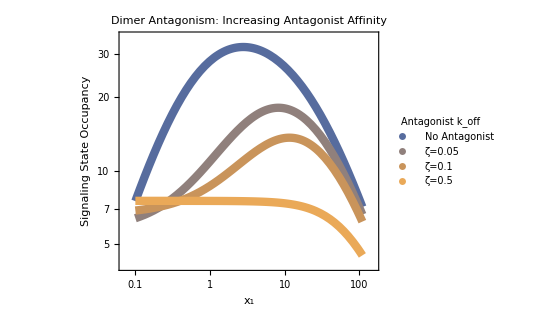

```mathematica
pops={Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},PlotLabel->"Dimer Antagonism:\nIncreasing Antagonist Affinity",PlotStyle->Join[Table[{contourcmap[[i]],Thickness[0.015]},{i,1,6}],{{Black,Dashed,Thickness[0.015]}}],AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}
};

FigS4C=Legended[
LogLogPlot[
{DiMixedSimple[0.1x1,0,0.1,0.2,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,2,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,10,0.1,0.2,100,1,0.01]},{x1,0.1,110},Evaluate@pops],

PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","ζ=0.05","ζ=0.1","ζ=0.5"},LegendMarkerSize->25,LegendLabel->"Antagonist k_off",LabelStyle->{Directive[FontSize->20]}]]
```

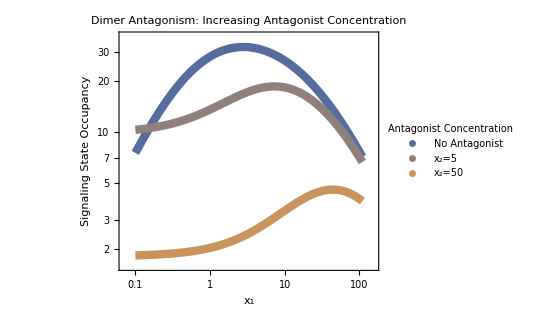

```mathematica
pops={Frame->{{True,False},{True,False}},FrameLabel->{"x_1","Signaling State Occupancy"},PlotLabel->"Dimer Antagonism:\nIncreasing Antagonist Concentration",PlotStyle->Join[Table[{contourcmap[[i]],Thickness[0.015]},{i,1,6}],{{Black,Dashed,Thickness[0.015]}}],AspectRatio->0.8,ImageSize->400,TicksStyle->Black,LabelStyle-> {Black,FontSize->20},Axes->{True,False}
};

FigS4D=Legended[
LogLogPlot[
{DiMixedSimple[0.1x1,0,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,5,0.1,1,100,1,0.01],
DiMixedSimple[0.1x1,50,0.1,1,100,1,0.01]},{x1,0.1,110},Evaluate@pops],

PointLegend[Table[contourcmap[[i]],{i,1,6}],{"No Antagonist","x_2=5","x_2=50"},LegendMarkerSize->25,LegendLabel->"Antagonist Concentration",LabelStyle->{Directive[FontSize->20]}]]
```

### Export Figures

```mathematica
savedir=FileNameJoin[{NotebookDirectory[]}];
SetDirectory[savedir];
```

```mathematica
Export["FigS2A.pdf",FigEntropyB];(*Example*)
```

## Approximate Expressions

#### Dimer

```mathematica
t1=Simplify[SNRDimerNonEq/.{c->koff/kon x,kf->koff/g},Assumptions->asmps];

Assuming[asmps,Simplify[Series[Evaluate[t1/.g->1/q],{q,0,1}]]]


Assuming[asmps,Simplify[Series[t1,{g,0,1}]]]
```

(ⅇ^(-δ21/2) RT √((kp t x)/(1+kp t)) √q)/(1+x)+O[q]^(3/2)

(√(kp RT t))/(√2)-((ⅇ^(δ21/2) kp t (2+kp t+2 x)) √g)/(8 √(kp t x))+(ⅇ^δ21 kp t (4 kp t+3 kp^2 t^2+4 (1+x)^2) g)/(64 √2 √(kp RT t) x)+O[g]^(3/2)

```mathematica
(ⅇ^(-δ21/2)  x)/(√RT √(kp t (1+kp t) x g/RT) (1+x))
```

### State energy for multimer

0=ϵ-μ-k_B T ln[A/(R_i a_0)]+i k_B T ln[A/(R_0 a_0)]
and
R_i=(k_on c)/(i! k_f)((k_f R_0)/(k_off A))^i

Substituting:
0=ϵ-μ-k_B T ln[A/((k_on c)/(i! k_f)(k_f[R_0]/k_off)^i a_0)]+i k_B T ln[1/([R_0]a_0)]

Combining and simplifying:

ϵ=μ+k_B T ln[A/((k_on c)/(i! k_f)(k_f[R_0]/k_off)^i a_0)]- k_B T ln[(1/([R_0]a_0))^i]
ϵ=μ+k_B T ln[(A ([R_0]a_0)^i)/((k_on c)/(i! k_f)(k_f[R_0]/k_off)^i a_0)]
ϵ=μ+k_B T ln[((A [R_0])^i a_0^i)/((k_on c)/(i! k_f)((k_f^i[R_0])^i)/k_off^i a_0)]
ϵ=μ+k_B T ln[(A i!)/(k_on c)(a_0^(i-1)k_off^i)/k_f^(i-1)]
ϵ=μ+k_B T ln[i!A K_D/c(a_0^(i-1)k_off^(i-1))/k_f^(i-1)]